This shows how to call the connecting routine with Mathematica

First compile the source using 

cd Ultraspherical
mcc ultrasolve.tm UltrasphericalMathLink.cpp AdaptiveQR.cpp FilledBandedOperator.cpp UltrasphericalOperator.cpp Operator.cpp -o UltrasphericalMathLink


We can now install the compiled file:

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];
```

This installs UltrasphericalSolve[{a0,...,an}], which solves the ODE u’’ + (a0 T0(x) + ... + an Tn(x)) u = 0, u(-1) = 1, u(1) = 0.

```mathematica
a=Exp[#]&//Fun;b=AiryAi[#]&//Fun;f=Cos[Cos[#]]&//Fun;
```

```mathematica
Install[NotebookDirectory[]<>"Ultraspherical/UltrasphericalMathLink"];U=PoissonSolve[{{0.0625,0.07,1},{2,3,4}}]
```

{{0.0625,0.07,1.},{2.,3.,4.}}

```mathematica
U
```

{{-0.241005,-0.370775,-0.0284173,-0.00354618,-0.000824185,-0.000263595,-0.000101898,-0.0000448134,-0.0000215838,-0.000011072,-5.91504×10^-6,-3.22979×10^-6,-1.77475×10^-6,-9.69345×10^-7,-5.21352×10^-7,-2.74277×10^-7,-1.40507×10^-7,-6.98927×10^-8,-3.37044×10^-8,-1.57443×10^-8,-7.12251×10^-9,-3.12066×10^-9,-1.32458×10^-9,-5.44843×10^-10,-2.17265×10^-10,-8.40196×10^-11,-3.15198×10^-11,-1.1474×10^-11,-4.05381×10^-12,-1.39028×10^-12,-4.6289×10^-13,-1.49627×10^-13,-4.69572×10^-14,-1.4306×10^-14,-4.23049×10^-15,-1.21397×10^-15,-3.3791×10^-16,-9.1189×10^-17,-2.38427×10^-17,-6.03675×10^-18,-1.48018×10^-18,-3.52224×10^-19,-8.19572×10^-20,-1.60512×10^-23,1.0437×10^-29},{-0.0572669,-0.150691,-0.0487509,-0.0117468,-0.00314585,-0.00103512,-0.000403893,-0.000178339,-0.0000860642,-0.0000441958,-0.000023625,-0.0000129045,-7.09247×10^-6,-3.8743×10^-6,-2.08391×10^-6,-1.09637×10^-6,-5.6167×10^-7,-2.79397×10^-7,-1.34736×10^-7,-6.29398×10^-8,-2.84733×10^-8,-1.24754×10^-8,-5.29526×10^-9,-2.17814×10^-9,-8.68569×10^-10,-3.35891×10^-10,-1.2601×10^-10,-4.58708×10^-11,-1.62064×10^-11,-5.55813×10^-12,-1.85057×10^-12,-5.98192×10^-13,-1.87729×10^-13,-5.71938×10^-14,-1.69131×10^-14,-4.85334×10^-15,-1.35094×10^-15,-3.64565×10^-16,-9.5321×10^-17,-2.41343×10^-17,-5.9176×10^-18,-1.40815×10^-18,-3.27673×10^-19,-7.60109×10^-20,-1.00948×10^-22,-4.43677×10^-30,7.18383×10^-34},{-0.012293,-0.0415309,-0.032301,-0.0145879,-0.00548775,-0.0020821,-0.000859335,-0.00038887,-0.000189949,-0.000098178,-0.0000526749,-0.0000288344,-0.0000158682,-8.67484×10^-6,-4.66826×10^-6,-2.45675×10^-6,-1.25882×10^-6,-6.26264×10^-7,-3.02033×10^-7,-1.41099×10^-7,-6.38348×10^-8,-2.79701×10^-8,-1.18725×10^-8,-4.88379×10^-9,-1.94757×10^-9,-7.53184×10^-10,-2.82566×10^-10,-1.02864×10^-10,-3.63436×10^-11,-1.24646×10^-11,-4.15017×10^-12,-1.34156×10^-12,-4.21027×10^-13,-1.28272×10^-13,-3.79325×10^-14,-1.08851×10^-14,-3.0299×10^-15,-8.17651×10^-16,-2.13786×10^-16,-5.41279×10^-17,-1.32717×10^-17,-3.15813×10^-18,-7.34908×10^-19,-1.70554×10^-19,-4.0802×10^-20,-1.81099×10^-22,1.39262×10^-31,-1.31655×10^-34,1.6668×10^-38},{-0.00281676,-0.0104226,-0.0140626,-0.010589,-0.00581999,-0.00279348,-0.00130887,-0.000631998,-0.000319355,-0.00016816,-0.0000911869,-0.00005023,-0.0000277467,-0.0000152032,-8.19279×10^-6,-4.31529×10^-6,-2.21231×10^-6,-1.10101×10^-6,-5.31125×10^-7,-2.48167×10^-7,-1.1229×10^-7,-4.92079×10^-8,-2.08899×10^-8,-8.59403×10^-9,-3.4275×10^-9,-1.32565×10^-9,-4.9738×10^-10,-1.8108×10^-10,-6.39836×10^-11,-2.19459×10^-11,-7.30748×10^-12,-2.36231×10^-12,-7.41411×10^-13,-2.25892×10^-13,-6.68026×10^-14,-1.91701×10^-14,-5.33611×10^-15,-1.44001×10^-15,-3.76502×10^-16,-9.53226×10^-17,-2.33715×10^-17,-5.56142×10^-18,-1.29428×10^-18,-3.0048×10^-19,-7.20014×10^-20,-8.06438×10^-22,-5.12962×10^-33,1.50313×10^-35,-1.01501×10^-38,1.16625×10^-42},{-0.000766464,-0.00295704,-0.005304,-0.00575053,-0.00441295,-0.00274248,-0.00153159,-0.000824289,-0.000444001,-0.000242686,-0.000134534,-0.0000750943,-0.0000418152,-0.0000230238,-0.0000124444,-6.5668×10^-6,-3.37052×10^-6,-1.67871×10^-6,-8.10234×10^-7,-3.78732×10^-7,-1.71424×10^-7,-7.51428×10^-8,-3.19081×10^-8,-1.31301×10^-8,-5.23778×10^-9,-2.02625×10^-9,-7.60399×10^-10,-2.7689×10^-10,-9.78551×10^-11,-3.3569×10^-11,-1.11794×10^-11,-3.61446×10^-12,-1.13452×10^-12,-3.45697×10^-13,-1.0224×10^-13,-2.93409×10^-14,-8.16741×10^-15,-2.20405×10^-15,-5.76245×10^-16,-1.45883×10^-16,-3.57654×10^-17,-8.51047×10^-18,-1.98101×10^-18,-4.60283×10^-19,-1.10808×10^-19,-2.7539×10^-20,-6.13556×10^-22,-1.73959×10^-35,-1.13781×10^-37,2.11207×10^-40,-1.1615×10^-43,1.19812×10^-47},{-0.00025545,-0.00100454,-0.00203504,-0.00275749,-0.00272888,-0.00214192,-0.00144245,-0.000888923,-0.000524392,-0.000303822,-0.000174686,-0.0000997402,-0.0000563227,-0.0000312814,-0.0000169983,-8.99985×10^-6,-4.62913×10^-6,-2.30881×10^-6,-1.11545×10^-6,-5.2179×10^-7,-2.36321×10^-7,-1.03645×10^-7,-4.40327×10^-8,-1.81276×10^-8,-7.23453×10^-9,-2.79986×10^-9,-1.05112×10^-9,-3.82893×10^-10,-1.35363×10^-10,-4.64503×10^-11,-1.54735×10^-11,-5.00405×10^-12,-1.57103×10^-12,-4.78788×10^-13,-1.41621×10^-13,-4.06464×10^-14,-1.13149×10^-14,-3.05339×10^-15,-7.98244×10^-16,-2.02059×10^-16,-4.95304×10^-17,-1.17854×10^-17,-2.74446×10^-18,-6.38654×10^-19,-1.54316×10^-19,-3.86016×10^-20,-1.55215×10^-21,-1.30371×10^-37,1.68256×10^-39,-6.85471×10^-42,1.02797×10^-44,-5.06406×10^-48,4.93772×10^-52},{-0.00010022,-0.000397361,-0.000846947,-0.00129475,-0.00152145,-0.00143796,-0.00114874,-0.000814586,-0.00053417,-0.00033349,-0.000201639,-0.000118975,-0.0000686125,-0.000038617,-0.0000211607,-0.0000112631,-5.81307×10^-6,-2.90595×10^-6,-1.40624×10^-6,-6.58646×10^-7,-2.98615×10^-7,-1.31087×10^-7,-5.57385×10^-8,-2.29651×10^-8,-9.17203×10^-9,-3.55224×10^-9,-1.33449×10^-9,-4.86422×10^-10,-1.72064×10^-10,-5.90758×10^-11,-1.96888×10^-11,-6.36996×10^-12,-2.00059×10^-12,-6.09888×10^-13,-1.80442×10^-13,-5.17965×10^-14,-1.44199×10^-14,-3.89117×10^-15,-1.01713×10^-15,-2.57404×10^-16,-6.30807×10^-17,-1.50089×10^-17,-3.49767×10^-18,-8.16195×10^-19,-1.98506×10^-19,-5.02237×10^-20,-3.26706×10^-21,-5.62325×10^-40,-1.28362×10^-41,9.86041×10^-44,-3.12386×10^-46,4.06193×10^-49,-1.83833×10^-52,1.70508×10^-56},{-0.0000442442,-0.000176088,-0.000384143,-0.000625049,-0.00081661,-0.000882232,-0.000810268,-0.000652928,-0.000476235,-0.000322746,-0.000207114,-0.000127349,-0.0000754948,-0.0000432638,-0.0000239849,-0.0000128631,-6.6721×10^-6,-3.34688×10^-6,-1.62371×10^-6,-7.62021×10^-7,-3.46067×10^-7,-1.52148×10^-7,-6.47844×10^-8,-2.67275×10^-8,-1.06881×10^-8,-4.14436×10^-9,-1.55868×10^-9,-5.68736×10^-10,-2.01376×10^-10,-6.9201×10^-11,-2.30816×10^-11,-7.4729×10^-12,-2.34841×10^-12,-7.16277×10^-13,-2.11999×10^-13,-6.08707×10^-14,-1.69479×10^-14,-4.57307×10^-15,-1.19508×10^-15,-3.02317×10^-16,-7.40551×10^-17,-1.76188×10^-17,-4.11133×10^-18,-9.64061×10^-19,-2.37105×10^-19,-6.11396×10^-20,-5.8659×10^-21,-1.51808×10^-42,5.66084×10^-44,-7.41848×10^-46,4.29486×10^-48,-1.14853×10^-50,1.3403×10^-53,-5.65197×10^-57,5.00647×10^-61},{-0.0000211174,-0.0000842049,-0.000185852,-0.000312489,-0.000434468,-0.000513095,-0.000522912,-0.000468091,-0.000375587,-0.000275588,-0.00018812,-0.000121041,-0.0000740844,-0.0000433916,-0.0000244111,-0.0000132216,-6.90487×10^-6,-3.48066×10^-6,-1.69497×10^-6,-7.97923×10^-7,-3.6335×10^-7,-1.6014×10^-7,-6.83448×10^-8,-2.82581×10^-8,-1.13237×10^-8,-4.39946×10^-9,-1.65769×10^-9,-6.05907×10^-10,-2.14878×10^-10,-7.39478×10^-11,-2.46969×10^-11,-8.00498×10^-12,-2.51808×10^-12,-7.68643×10^-13,-2.27637×10^-13,-6.53866×10^-14,-1.82079×10^-14,-4.91239×10^-15,-1.28319×10^-15,-3.24378×10^-16,-7.94005×10^-17,-1.88895×10^-17,-4.41863×10^-18,-1.04507×10^-18,-2.62016×10^-19,-6.9687×10^-20,-9.09528×10^-21,-2.71568×10^-45,-1.55521×10^-46,3.23599×10^-48,-3.11299×10^-50,1.48713×10^-52,-3.49887×10^-55,3.73803×10^-58,-1.48186×10^-61,1.25704×10^-65},{-0.0000103582,-0.0000413447,-0.0000918201,-0.000157148,-0.000226425,-0.000282727,-0.000309478,-0.000299699,-0.00025971,-0.000204107,-0.000147479,-0.0000991962,-0.0000627546,-0.0000376439,-0.0000215411,-0.0000118104,-6.22368×10^-6,-3.15923×10^-6,-1.54727×10^-6,-7.32013×10^-7,-3.34839×10^-7,-1.48195×10^-7,-6.3499×10^-8,-2.63541×10^-8,-1.05988×10^-8,-4.13185×10^-9,-1.56182×10^-9,-5.72557×10^-10,-2.03603×10^-10,-7.02398×10^-11,-2.351×10^-11,-7.63492×10^-12,-2.40559×10^-12,-7.35282×10^-13,-2.17973×10^-13,-6.26488×10^-14,-1.74485×10^-14,-4.70599×10^-15,-1.22822×10^-15,-3.10078×10^-16,-7.58015×10^-17,-1.80347×10^-17,-4.23926×10^-18,-1.01911×10^-18,-2.64481×10^-19,-7.40768×10^-20,-1.2995×10^-20,-1.73913×10^-21,-4.20635×10^-49,3.52044×10^-50,-1.07745×10^-51,1.56232×10^-53,-1.17712×10^-55,4.70015×10^-58,-9.63021×10^-61,9.21294×10^-64,-3.33603×10^-67,2.62302×10^-71},{-4.63818×10^-6,-0.0000185233,-0.0000412739,-0.0000713203,-0.000104824,-0.000135257,-0.000154891,-0.000158235,-0.000145046,-0.000120284,-0.0000911619,-0.000063827,-0.00004171,-0.0000256704,-0.0000149898,-8.35291×10^-6,-4.46111×10^-6,-2.29077×10^-6,-1.13354×10^-6,-5.41389×10^-7,-2.49862×10^-7,-1.11526×10^-7,-4.81743×10^-8,-2.0148×10^-8,-8.1619×10^-9,-3.20356×10^-9,-1.21861×10^-9,-4.49344×10^-10,-1.60636×10^-10,-5.56813×10^-11,-1.87158×10^-11,-6.10022×10^-12,-1.92795×10^-12,-5.90735×10^-13,-1.75434×10^-13,-5.04733×10^-14,-1.40593×10^-14,-3.78854×10^-15,-9.86845×10^-16,-2.48441×10^-16,-6.05742×10^-17,-1.44213×10^-17,-3.42916×10^-18,-8.54237×10^-19,-2.37417×10^-19,-7.25278×10^-20,-1.59005×10^-20,-2.65053×10^-21,4.82264×10^-52,-5.63173×10^-53,2.47904×10^-54,-5.29714×10^-56,6.09023×10^-58,-3.90338×10^-60,1.38568×10^-62,-2.60071×10^-65,2.32801×10^-68,-8.012×10^-72,6.05869×10^-76},{-9.43107×10^-7,-3.76796×10^-6,-8.41659×10^-6,-0.0000146485,-0.0000218605,-0.0000289614,-0.0000344862,-0.0000370633,-0.0000360472,-0.0000318579,-0.0000257457,-0.000019176,-0.0000132771,-8.61711×10^-6,-5.28196×10^-6,-3.07705×10^-6,-1.71214×10^-6,-9.13354×10^-7,-4.68388×10^-7,-2.31344×10^-7,-1.10195×10^-7,-5.06648×10^-8,-2.24989×10^-8,-9.65442×10^-9,-4.00463×10^-9,-1.60621×10^-9,-6.23106×10^-10,-2.33854×10^-10,-8.49266×10^-11,-2.98491×10^-11,-1.01546×10^-11,-3.34387×10^-12,-1.06577×10^-12,-3.28706×10^-13,-9.80596×10^-14,-2.82753×10^-14,-7.87283×10^-15,-2.11422×10^-15,-5.4708×10^-16,-1.36486×10^-16,-3.3016×10^-17,-7.89332×10^-18,-1.95516×10^-18,-5.43332×10^-19,-1.7903×10^-19,-6.44076×10^-20,-1.74017×10^-20,-3.45943×10^-21,-3.98153×10^-55,6.23592×10^-56,-3.8082×10^-57,1.15066×10^-58,-1.92052×10^-60,1.85331×10^-62,-1.04336×10^-64,3.35577×10^-67,-5.83452×10^-70,4.91858×10^-73,-1.61435×10^-76,1.17568×10^-80},{-2.68888×10^-9,-1.07429×10^-8,-2.39991×10^-8,-4.17808×10^-8,-6.23943×10^-8,-8.27874×10^-8,-9.88872×10^-8,-1.06907×10^-7,-1.05051×10^-7,-9.43717×10^-8,-7.81071×10^-8,-6.00892×10^-8,-4.33533×10^-8,-2.95709×10^-8,-1.91971×10^-8,-1.19239×10^-8,-7.11371×10^-9,-4.08747×10^-9,-2.26613×10^-9,-1.21358×10^-9,-6.28136×10^-10,-3.14269×10^-10,-1.51954×10^-10,-7.09641×10^-11,-3.19793×10^-11,-1.38864×10^-11,-5.79837×10^-12,-2.32123×10^-12,-8.86919×10^-13,-3.21197×10^-13,-1.08982×10^-13,-3.39188×10^-14,-9.25495×10^-15,-1.94324×10^-15,-1.19312×10^-16,1.75737×10^-16,1.36952×10^-16,7.05979×10^-17,2.99695×10^-17,1.09134×10^-17,3.31896×10^-18,7.17111×10^-19,-7.11476×10^-21,-1.27905×10^-19,-9.76634×10^-20,-5.10349×10^-20,-1.74332×10^-20,-4.02541×10^-21,2.52799×10^-58,-5.11135×10^-59,4.19592×10^-60,-1.73218×10^-61,4.03317×10^-63,-5.58206×10^-65,4.67994×10^-67,-2.36337×10^-69,6.97773×10^-72,-1.13302×10^-74,9.0391×10^-78,-2.83688×10^-81,1.99196×10^-85},{-3.63185×10^-12,-1.44275×10^-11,-3.10932×10^-11,-4.82945×10^-11,-5.29353×10^-11,-2.26786×10^-11,6.80655×10^-11,2.32215×10^-10,4.52386×10^-10,6.78594×10^-10,8.49226×10^-10,9.21564×10^-10,8.8932×10^-10,7.77969×10^-10,6.26662×10^-10,4.70881×10^-10,3.33622×10^-10,2.24827×10^-10,1.45111×10^-10,9.01867×10^-11,5.41912×10^-11,3.15749×10^-11,1.78767×10^-11,9.84871×10^-12,5.28461×10^-12,2.76321×10^-12,1.40826×10^-12,6.99542×10^-13,3.38624×10^-13,1.59666×10^-13,7.32863×10^-14,3.27151×10^-14,1.41851×10^-14,5.96338×10^-15,2.42441×10^-15,9.49576×10^-16,3.5623×10^-16,1.26788×10^-16,4.20919×10^-17,1.25882×10^-17,3.09605×10^-18,4.06332×10^-19,-1.74787×10^-19,-1.98298×10^-19,-1.2332×10^-19,-5.99904×10^-20,-2.18214×10^-20,-5.36003×10^-21,-1.55696×10^-61,3.98087×10^-62,-4.30621×10^-63,2.37033×10^-64,-7.4729×10^-66,1.43016×10^-67,-1.70513×10^-69,1.27202×10^-71,-5.85173×10^-74,1.60194×10^-76,-2.445×10^-79,1.85335×10^-82,-5.57463×10^-86,3.77792×10^-90},{1.37848×10^-14,7.12104×10^-14,3.80526×10^-13,1.80333×10^-12,6.47921×10^-12,1.81633×10^-11,4.1454×10^-11,7.92856×10^-11,1.29515×10^-10,1.83303×10^-10,2.27662×10^-10,2.5126×10^-10,2.49513×10^-10,2.25688×10^-10,1.88113×10^-10,1.46044×10^-10,1.06627×10^-10,7.38217×10^-11,4.88034×10^-11,3.09819×10^-11,1.89693×10^-11,1.12379×10^-11,6.45659×10^-12,3.60289×10^-12,1.95434×10^-12,1.03086×10^-12,5.28705×10^-13,2.6354×10^-13,1.27567×10^-13,5.98877×10^-14,2.72173×10^-14,1.19429×10^-14,5.0399×10^-15,2.03308×10^-15,7.76228×10^-16,2.7552×10^-16,8.75977×10^-17,2.25731×10^-17,2.79362×10^-18,-1.78639×10^-18,-1.98931×10^-18,-1.32609×10^-18,-7.39158×10^-19,-3.72077×10^-19,-1.73016×10^-19,-7.33551×10^-20,-2.62797×10^-20,-6.47797×10^-21,-7.48187×10^-65,-2.37469×10^-65,3.3272×10^-66,-2.39344×10^-67,9.97065×10^-69,-2.56221×10^-70,4.19096×10^-72,-4.41313×10^-74,2.97811×10^-76,-1.26197×10^-78,3.22724×10^-81,-4.65287×10^-84,3.36169×10^-87,-9.70878×10^-91,6.35611×10^-95},{1.1437×10^-17,6.52473×10^-18,-5.32538×10^-16,-4.02198×10^-15,-1.87752×10^-14,-7.01958×10^-14,-2.24545×10^-13,-6.16973×10^-13,-1.44273×10^-12,-2.85979×10^-12,-4.8256×10^-12,-7.00334×10^-12,-8.86181×10^-12,-9.92447×10^-12,-9.98569×10^-12,-9.15658×10^-12,-7.75284×10^-12,-6.13247×10^-12,-4.57798×10^-12,-3.2533×10^-12,-2.21659×10^-12,-1.45634×10^-12,-9.26873×10^-13,-5.73414×10^-13,-3.45731×10^-13,-2.03547×10^-13,-1.17178×10^-13,-6.6027×10^-14,-3.64418×10^-14,-1.97111×10^-14,-1.04526×10^-14,-5.43594×10^-15,-2.77315×10^-15,-1.38809×10^-15,-6.81856×10^-16,-3.28761×10^-16,-1.55619×10^-16,-7.23305×10^-17,-3.30186×10^-17,-1.48081×10^-17,-6.52675×10^-18,-2.82779×10^-18,-1.20375×10^-18,-5.02261×10^-19,-2.03758×10^-19,-7.84869×10^-20,-2.68641×10^-20,-6.38604×10^-21,-2.53399×10^-68,9.85252×10^-69,-1.76306×10^-69,1.63133×10^-70,-8.80348×10^-72,2.96621×10^-73,-6.4682×10^-75,9.28144×10^-77,-8.78509×10^-79,5.42816×10^-81,-2.1366×10^-83,5.13385×10^-86,-7.01944×10^-89,4.8464×10^-92,-1.34604×10^-95,8.5198×10^-100},{3.00111×10^-20,9.64525×10^-20,-3.85492×10^-19,-1.18477×10^-17,-1.28549×10^-16,-8.44556×10^-16,-3.89588×10^-15,-1.36459×10^-14,-3.79871×10^-14,-8.65461×10^-14,-1.64909×10^-13,-2.67654×10^-13,-3.763×10^-13,-4.65615×10^-13,-5.14733×10^-13,-5.15598×10^-13,-4.74077×10^-13,-4.04852×10^-13,-3.24489×10^-13,-2.46332×10^-13,-1.78506×10^-13,-1.24286×10^-13,-8.35869×10^-14,-5.45303×10^-14,-3.46213×10^-14,-2.14453×10^-14,-1.29836×10^-14,-7.69311×10^-15,-4.46536×10^-15,-2.54058×10^-15,-1.41747×10^-15,-7.75754×10^-16,-4.1652×10^-16,-2.19429×10^-16,-1.13429×10^-16,-5.75362×10^-17,-2.86398×10^-17,-1.39917×10^-17,-6.71102×10^-18,-3.16244×10^-18,-1.46543×10^-18,-6.6781×10^-19,-2.98324×10^-19,-1.2942×10^-19,-5.30261×10^-20,-1.88679×10^-20,-4.45395×10^-21,-6.11681×10^-72,-2.87635×10^-72,6.63505×10^-73,-8.02407×10^-74,5.69136×10^-75,-2.54503×10^-76,7.46518×10^-78,-1.4662×10^-79,1.94246×10^-81,-1.72961×10^-83,1.0201×10^-85,-3.87722×10^-88,9.08025×10^-91,-1.21935×10^-93,8.32068×10^-97,-2.29617×10^-100,1.45048×10^-104},{5.78256×10^-24,-1.55368×10^-23,-3.89413×10^-22,2.57474×10^-21,6.08663×10^-20,4.69657×10^-19,2.27907×10^-18,8.08885×10^-18,2.24385×10^-17,5.05882×10^-17,9.54999×10^-17,1.55162×10^-16,2.22906×10^-16,2.90422×10^-16,3.50472×10^-16,3.97413×10^-16,4.26632×10^-16,4.34765×10^-16,4.20887×10^-16,3.8742×10^-16,3.39751×10^-16,2.84722×10^-16,2.28865×10^-16,1.77158×10^-16,1.32571×10^-16,9.62433×10^-17,6.79935×10^-17,4.68652×10^-17,3.158×10^-17,2.08372×10^-17,1.34783×10^-17,8.55388×10^-18,5.32933×10^-18,3.2605×10^-18,1.95839×10^-18,1.15353×10^-18,6.64367×10^-19,3.71761×10^-19,1.99555×10^-19,1.00431×10^-19,4.57484×10^-20,1.81542×10^-20,6.32823×10^-21,2.12594×10^-21,5.17245×10^-22,-3.63115×10^-76,-1.62688×10^-76,4.56148×10^-77,-7.16821×10^-78,6.72623×10^-79,-4.03087×10^-80,1.60603×10^-81,-4.3512×10^-83,8.10054×10^-85,-1.03719×10^-86,9.06037×10^-89,-5.30476×10^-91,2.02064×10^-93,-4.77929×10^-96,6.52308×10^-99,-4.54816×10^-102,1.28812×10^-105,-8.38224×10^-110},{2.04247×10^-26,2.13597×10^-26,-5.8661×10^-25,7.33746×10^-24,4.4539×10^-22,8.09169×10^-21,8.21408×10^-20,5.53495×10^-19,2.70549×10^-18,1.01132×10^-17,2.99529×10^-17,7.22197×10^-17,1.45037×10^-16,2.47628×10^-16,3.66209×10^-16,4.77202×10^-16,5.5656×10^-16,5.89287×10^-16,5.73736×10^-16,5.19575×10^-16,4.42126×10^-16,3.56673×10^-16,2.74887×10^-16,2.0372×10^-16,1.45975×10^-16,1.01585×10^-16,6.89043×10^-17,4.56827×10^-17,2.96671×10^-17,1.89012×10^-17,1.18264×10^-17,7.2724×10^-18,4.39709×10^-18,2.61444×10^-18,1.52775×10^-18,8.75599×10^-19,4.89726×10^-19,2.64238×10^-19,1.34163×10^-19,6.08648×10^-20,2.20865×10^-20,4.81128×10^-21,8.68741×10^-79,5.88863×10^-79,-2.34609×10^-79,5.24049×10^-80,-6.89902×10^-81,5.77412×10^-82,-3.22412×10^-83,1.23451×10^-84,-3.28883×10^-86,6.12728×10^-88,-7.95996×10^-90,7.13274×10^-92,-4.32195×10^-94,1.7161×10^-96,-4.25641×10^-99,6.12213×10^-102,-4.51698×10^-105,1.35843×10^-108,-9.41416×10^-113},{-2.62281×10^-30,1.12666×10^-29,3.97495×10^-28,-6.46073×10^-27,-6.72958×10^-25,-1.38497×10^-23,-1.47408×10^-22,-1.01935×10^-21,-5.08833×10^-21,-1.94485×10^-20,-5.91237×10^-20,-1.47012×10^-19,-3.05922×10^-19,-5.43512×10^-19,-8.3933×10^-19,-1.14503×10^-18,-1.40025×10^-18,-1.55517×10^-18,-1.58685×10^-18,-1.50242×10^-18,-1.33077×10^-18,-1.10956×10^-18,-8.7405×10^-19,-6.50853×10^-19,-4.56382×10^-19,-2.98373×10^-19,-1.78462×10^-19,-9.44604×10^-20,-4.17245×10^-20,-1.37302×10^-20,-2.53178×10^-21,-7.03505×10^-82,6.32026×10^-82,-4.0839×10^-82,1.75607×10^-82,-4.62332×10^-83,7.61101×10^-84,-8.26767×10^-85,6.1482×10^-86,-3.19462×10^-87,1.17114×10^-88,-3.03399×10^-90,5.52388×10^-92,-6.97794×10^-94,5.98654×10^-96,-3.37631×10^-98,1.19213×10^-100,-2.44472×10^-103,2.57423×10^-106,-1.10547×10^-109,1.09422×10^-113},{-5.00658×10^-33,-3.55948×10^-32,-1.50757×10^-31,6.11323×10^-31,-1.26809×10^-28,-3.06885×10^-27,-3.17075×10^-26,-1.91178×10^-25,-7.3636×10^-25,-1.83693×10^-24,-2.86262×10^-24,-2.51452×10^-24,-9.34351×10^-25,2.51596×10^-82,1.51304×10^-82,-5.06696×10^-83,6.80165×10^-84,1.76898×10^-84,-1.14901×10^-84,3.08013×10^-85,-5.30941×10^-86,6.45873×10^-87,-5.72031×10^-88,3.72257×10^-89,-1.77619×10^-90,6.15235×10^-92,-1.52085×10^-93,2.6166×10^-95,-3.02346×10^-97,2.22905×10^-99,-9.70914×10^-102,2.20598×10^-104,-2.07494×10^-107,4.56489×10^-111},{3.85168×10^-36,1.45053×10^-35,2.10832×10^-35,1.42223×10^-75,6.82074×10^-77,-4.65897×10^-78,1.94601×10^-79,-4.75359×10^-81,-9.49848×10^-85,6.76566×10^-84,-4.08883×10^-85,1.6343×10^-86,-5.12977×10^-88,1.33282×10^-89,-2.92639×10^-91,5.46419×10^-93,-8.64446×10^-95,1.14316×10^-96,-1.23309×10^-98,1.04478×10^-100,-6.58324×10^-103,2.8483×10^-105,-7.47463×10^-108,9.52337×10^-111,-3.42645×10^-114}}

```mathematica
f[{___?{___Real}}]=3
```

3

```mathematica
f[{{0.0625,0.0625}}]
```

f[{{0.0625,0.0625}}]

```mathematica
?..
```

p.. or Repeated[p] is a pattern object that represents a sequence of one or more expressions, each matching p. 
Repeated[p,max] represents up to max expressions matching p.
Repeated[p,{min,max}] represents between min and max expressions matching p.
Repeated[p,{n}] represents exactly n expressions matching p.

```mathematica
Length/@U
```

{45,47,49,50,52,53,54,55,56,58,59,60,61,62,63,64,64,63,61,51,34,25}

```mathematica
Norm/@U
```

{0.443146,0.168858,0.0562805,0.0216882,0.0100417,0.00530446,0.00306358,0.00187021,0.001166,0.000706011,0.000368887,0.0000884137,2.59598×10^-7,2.12297×10^-9,6.03597×10^-10,2.41096×10^-11,1.26924×10^-12,1.21039×10^-15,1.47859×10^-15,4.01427×10^-18,4.39824×10^-24,2.58793×10^-35}

```mathematica
U⟦1⟧
```

```mathematica
Norm/@U
```

{0.443146,0.168858,0.0562805,0.0216882,0.0100417,0.00530446,0.00306358,0.00187021,0.001166,0.000706011,0.000368887,0.0000884132,2.596×10^-7,2.12306×10^-9,6.03598×10^-10,2.41096×10^-11,1.26924×10^-12,1.21041×10^-15,1.47859×10^-15,4.01443×10^-18,4.02578×10^-24,2.58793×10^-35}

```mathematica
Last/@U
```

{4.90713×10^-31,3.59567×10^-35,9.982×10^-40,1.81486×10^-44,8.67035×10^-49,8.65897×10^-54,2.79094×10^-58,7.81316×10^-63,1.91763×10^-67,4.14313×10^-72,7.88908×10^-77,1.32347×10^-81,1.95339×10^-86,2.61791×10^-91,3.115×10^-96,3.16051×10^-101,1.43476×10^-104,-4.79321×10^-111,-9.42364×10^-113,1.09436×10^-113,-1.58347×10^-111,-3.42645×10^-114}

```mathematica
U⟦1⟧
```

{-9.43102×10^-7,-3.76794×10^-6,-8.41655×10^-6,-0.0000146485,-0.0000218604,-0.0000289613,-0.000034486,-0.0000370631,-0.000036047,-0.0000318577,-0.0000257455,-0.0000191759,-0.000013277,-8.61707×10^-6,-5.28194×10^-6,-3.07704×10^-6,-1.71214×10^-6,-9.1335×10^-7,-4.68385×10^-7,-2.31343×10^-7,-1.10195×10^-7,-5.06646×10^-8,-2.24987×10^-8,-9.65438×10^-9,-4.00461×10^-9,-1.6062×10^-9,-6.23103×10^-10,-2.33853×10^-10,-8.49262×10^-11,-2.9849×10^-11,-1.01545×10^-11,-3.34385×10^-12,-1.06577×10^-12,-3.28705×10^-13,-9.80591×10^-14,-2.82751×10^-14,-7.87279×10^-15,-2.1142×10^-15,-5.47075×10^-16,-1.36485×10^-16,-3.30156×10^-17,-7.89337×10^-18,-1.95561×10^-18,-5.44523×10^-19,-1.81865×10^-19,-7.07726×10^-20,-2.91335×10^-20,-1.16492×10^-20,-4.16773×10^-21,-9.31685×10^-22,-1.04221×10^-55,1.46484×10^-56,-8.17048×10^-58,2.27527×10^-59,-3.51619×10^-61,3.15067×10^-63,-1.65034×10^-65,4.94676×10^-68,-8.0263×10^-71,6.32203×10^-74,-1.94088×10^-77,1.32347×10^-81}

```mathematica
U//Length
```

22

```mathematica
X=BlockDiagonalMatrix[{({{0, 0}, {0, 0}}),PadRight[U,{U//Length,Length/@U//Max}]}];
```

```mathematica
X//ArrayPlot
```

-Graphics-

```mathematica
n=50;
```

```mathematica
DerivativeMatrix[2,n].X.ConversionMatrix[2,n]ᵀ+ConversionMatrix[2,n].X.DerivativeMatrix[2,n]ᵀ//Chop//MatrixForm
```

(1.25822 | 1.99596 | -0.022197 | -0.183192 | -0.0152129 | -0.00343752 | -0.00139316 | -0.000676797 | -0.000360378 | -0.000203038 | -0.000118271 | -0.0000699502 | -0.0000413926 | -0.0000242234 | -0.0000138975 | -7.76883×10^-6 | -4.21431×10^-6 | -2.21302×10^-6 | -1.12348×10^-6 | -5.51117×10^-7 | -2.61222×10^-7 | -1.1967×10^-7 | -5.30094×10^-8 | -2.2716×10^-8 | -9.42188×10^-9 | -3.78421×10^-9 | -1.47241×10^-9 | -5.55204×10^-10 | -2.02946×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.264809 | 0.661482 | 0.151037 | -0.068038 | -0.0207615 | -0.00448877 | -0.00126356 | -0.000499257 | -0.00024182 | -0.000130246 | -0.0000741492 | -0.0000433159 | -0.0000254561 | -0.0000148404 | -8.49732×10^-6 | -4.74593×10^-6 | -2.57409×10^-6 | -1.3521×10^-6 | -6.86813×10^-7 | -3.37163×10^-7 | -1.59945×10^-7 | -7.33389×10^-8 | -3.25165×10^-8 | -1.39472×10^-8 | -5.79031×10^-9 | -2.32782×10^-9 | -9.06599×10^-10 | -3.42183×10^-10 | -1.25202×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.12537 | -0.196095 | 0.074904 | 0.00863439 | -0.00818896 | -0.00417192 | -0.00140308 | -0.000481923 | -0.000194474 | -0.0000916907 | -0.000048016 | -0.0000266768 | -0.0000152209 | -8.72484×10^-6 | -4.95113×10^-6 | -2.75456×10^-6 | -1.49304×10^-6 | -7.85358×10^-7 | -4.00004×10^-7 | -1.97044×10^-7 | -9.38379×10^-8 | -4.32037×10^-8 | -1.92359×10^-8 | -8.28577×10^-9 | -3.45449×10^-9 | -1.39466×10^-9 | -5.45474×10^-10 | -2.0676×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0310306 | -0.0746437 | 0.000315841 | 0.0117833 | 0.00208194 | -0.00130807 | -0.00104066 | -0.00048366 | -0.000204519 | -0.0000905923 | -0.0000436251 | -0.0000225927 | -0.0000122695 | -6.81896×10^-6 | -3.80478×10^-6 | -2.10211×10^-6 | -1.13911×10^-6 | -6.01638×10^-7 | -3.08503×10^-7 | -1.53231×10^-7 | -7.36356×10^-8 | -3.42214×10^-8 | -1.5381×10^-8 | -6.68753×10^-9 | -2.814×10^-9 | -1.14645×10^-9 | -4.52439×10^-10 | -1.73029×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00889654 | -0.0173664 | -0.00890642 | 0.00154362 | 0.00258915 | 0.000659635 | -0.000231513 | -0.000293453 | -0.000176971 | -0.0000899416 | -0.0000445807 | -0.0000226978 | -0.0000119879 | -6.51151×10^-6 | -3.58545×10^-6 | -1.9732×10^-6 | -1.07273×10^-6 | -5.71151×10^-7 | -2.96073×10^-7 | -1.4888×10^-7 | -7.24711×10^-8 | -3.41165×10^-8 | -1.55281×10^-8 | -6.8343×10^-9 | -2.90973×10^-9 | -1.19896×10^-9 | -4.78374×10^-10 | -1.84906×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0031652 | -0.0039501 | -0.00401193 | -0.00140769 | 0.000600901 | 0.000720296 | 0.000237897 | -0.0000359232 | -0.00008958 | -0.0000678282 | -0.0000404499 | -0.0000224102 | -0.0000122567 | -6.7529×10^-6 | -3.75029×10^-6 | -2.0827×10^-6 | -1.14489×10^-6 | -6.17369×10^-7 | -3.24378×10^-7 | -1.65338×10^-7 | -8.15476×10^-8 | -3.88725×10^-8 | -1.79026×10^-8 | -7.96704×10^-9 | -3.42748×10^-9 | -1.42623×10^-9 | -5.74368×10^-10 | -2.23987×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00136229 | -0.00119796 | -0.001341 | -0.00103316 | -0.000248607 | 0.000229156 | 0.000239064 | 0.0000955181 | 5.74751×10^-7 | -0.0000284049 | -0.0000269145 | -0.0000185805 | -0.0000114725 | -6.78578×10^-6 | -3.94048×10^-6 | -2.25674×10^-6 | -1.2697×10^-6 | -6.97571×10^-7 | -3.72287×10^-7 | -1.92318×10^-7 | -9.59731×10^-8 | -4.62275×10^-8 | -2.14901×10^-8 | -9.64536×10^-9 | -4.1821×10^-9 | -1.75291×10^-9 | -7.10732×10^-10 | -2.78938×10^-10 | -1.06025×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000667523 | -0.000488017 | -0.000467263 | -0.000474434 | -0.000293497 | -0.0000388352 | 0.0000943316 | 0.0000916108 | 0.0000424847 | 5.90513×10^-6 | -8.86382×10^-6 | -0.000011031 | -8.82765×10^-6 | -6.0575×10^-6 | -3.85673×10^-6 | -2.34307×10^-6 | -1.37044×10^-6 | -7.72978×10^-7 | -4.20234×10^-7 | -2.20068×10^-7 | -1.10989×10^-7 | -5.39235×10^-8 | -2.52524×10^-8 | -1.14074×10^-8 | -4.97506×10^-9 | -2.09648×10^-9 | -8.54283×10^-10 | -3.36846×10^-10 | -1.286×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000352523 | -0.000236157 | -0.000189363 | -0.000199715 | -0.000173969 | -0.0000883005 | 1.40754×10^-6 | 0.0000432715 | 0.0000401089 | 0.0000208205 | 5.04058×10^-6 | -2.72583×10^-6 | -4.8883×10^-6 | -4.48456×10^-6 | -3.33535×10^-6 | -2.22072×10^-6 | -1.37328×10^-6 | -8.01763×10^-7 | -4.45544×10^-7 | -2.36738×10^-7 | -1.20623×10^-7 | -5.90578×10^-8 | -2.783×10^-8 | -1.26395×10^-8 | -5.539×10^-9 | -2.34451×10^-9 | -9.59336×10^-10 | -3.79757×10^-10 | -1.45522×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000189961 | -0.000122092 | -0.0000865649 | -0.0000863435 | -0.0000862106 | -0.0000647316 | -0.0000259646 | 7.55726×10^-6 | 0.0000212636 | 0.0000184109 | 9.63055×10^-6 | 2.28445×10^-6 | -1.57916×10^-6 | -2.74829×10^-6 | -2.54344×10^-6 | -1.89103×10^-6 | -1.24369×10^-6 | -7.52435×10^-7 | -4.27069×10^-7 | -2.29909×10^-7 | -1.18165×10^-7 | -5.82241×10^-8 | -2.75804×10^-8 | -1.25844×10^-8 | -5.53905×10^-9 | -2.3545×10^-9 | -9.67415×10^-10 | -3.84499×10^-10 | -1.47912×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000093168 | -0.0000608927 | -0.0000458587 | -0.000051689 | -0.0000647638 | -0.0000742517 | -0.0000734367 | -0.0000640355 | -0.0000524352 | -0.0000426896 | -0.0000348291 | -0.0000276009 | -0.0000206037 | -0.0000142973 | -9.22268×10^-6 | -5.56366×10^-6 | -3.16219×10^-6 | -1.70498×10^-6 | -8.77021×10^-7 | -4.32318×10^-7 | -2.0493×10^-7 | -9.36695×10^-8 | -4.13737×10^-8 | -1.7691×10^-8 | -7.33362×10^-9 | -2.9508×10^-9 | -1.15355×10^-9 | -4.38464×10^-10 | -1.62128×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0000215591 | -0.000019457 | -0.0000279656 | -0.0000497927 | -0.0000814068 | -0.000115704 | -0.000142429 | -0.000153218 | -0.000146208 | -0.000125892 | -0.000099371 | -0.0000728154 | -0.0000499854 | -0.0000323535 | -0.0000198408 | -0.0000115739 | -6.44443×10^-6 | -3.43548×10^-6 | -1.75806×10^-6 | -8.6556×10^-7 | -4.10768×10^-7 | -1.88197×10^-7 | -8.33507×10^-8 | -3.57233×10^-8 | -1.48293×10^-8 | -5.96662×10^-9 | -2.3282×10^-9 | -8.81433×10^-10 | -3.23876×10^-10 | -1.15529×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-7.74598×10^-7 | -4.30341×10^-6 | -0.000012694 | -0.000027388 | -0.0000482921 | -0.0000726939 | -0.0000951409 | -0.00010935 | -0.000111379 | -0.000101607 | -0.0000840116 | -0.0000637241 | -0.000044846 | -0.0000295708 | -0.0000184172 | -0.0000109031 | -6.16478×10^-6 | -3.34089×10^-6 | -1.73982×10^-6 | -8.72287×10^-7 | -4.21632×10^-7 | -1.9669×10^-7 | -8.86258×10^-8 | -3.85965×10^-8 | -1.62546×10^-8 | -6.6228×10^-9 | -2.6116×10^-9 | -9.97056×10^-10 | -3.68642×10^-10 | -1.32032×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1.34811×10^-7 | -8.07431×10^-7 | -2.40465×10^-6 | -5.23139×10^-6 | -9.36842×10^-6 | -0.0000144803 | -0.000019706 | -0.0000238264 | -0.0000257486 | -0.0000250325 | -0.0000220695 | -0.0000178083 | -0.000013279 | -9.23431×10^-6 | -6.03787×10^-6 | -3.73741×10^-6 | -2.20203×10^-6 | -1.24003×10^-6 | -6.69434×10^-7 | -3.47213×10^-7 | -1.73285×10^-7 | -8.33079×10^-8 | -3.86121×10^-8 | -1.72644×10^-8 | -7.45072×10^-9 | -3.10504×10^-9 | -1.2501×10^-9 | -4.86413×10^-10 | -1.82989×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.56788×10^-10 | -2.14227×10^-9 | -6.38243×10^-9 | -1.38915×10^-8 | -2.49024×10^-8 | -3.85717×10^-8 | -5.27052×10^-8 | -6.41901×10^-8 | -7.02109×10^-8 | -6.95353×10^-8 | -6.29449×10^-8 | -5.26076×10^-8 | -4.09944×10^-8 | -3.00467×10^-8 | -2.08665×10^-8 | -1.38105×10^-8 | -8.74987×10^-9 | -5.32404×10^-9 | -3.11843×10^-9 | -1.76106×10^-9 | -9.59849×10^-10 | -5.05217×10^-10 | -2.56869×10^-10 | -1.26151×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.28617×10^-10 | 2.81503×10^-10 | 4.68169×10^-10 | 6.43679×10^-10 | 7.61811×10^-10 | 7.96775×10^-10 | 7.51256×10^-10 | 6.49008×10^-10 | 5.20711×10^-10 | 3.92394×10^-10 | 2.8032×10^-10 | 1.91264×10^-10 | 1.25374×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.18574×10^-10 | 1.60838×10^-10 | 1.92546×10^-10 | 2.06196×10^-10 | 2.00114×10^-10 | 1.78175×10^-10 | 1.47188×10^-10 | 1.1395×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

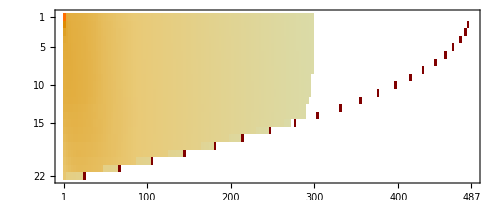

```mathematica
U//Abs//MatrixPlot
```

```mathematica
"3"
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},{10}]
```

{-0.247874,-0.594583,2.30122,-0.419138,-0.0549055,0.0139635,0.00157663,-0.0002374,-0.000019297,-5.1177×10^-6,-4.89701×10^-7,2.82999×10^-7,4.26803×10^-8,-1.91736×10^-9,-9.51222×10^-10,-1.61885×10^-10,-1.14567×10^-11,3.43466×10^-12,9.12297×10^-13,7.22144×10^-14,-6.22647×10^-15,-3.03866×10^-15,-4.84882×10^-16,-1.79416×10^-17,8.10583×10^-18,1.95887×10^-18,2.08444×10^-19,-3.09281×10^-21,-3.06823×10^-19,-6.54872×10^-20,-8.98754×10^-21,-9.42825×10^-22,-8.00475×10^-23,-6.26197×10^-24,-3.77888×10^-25,-1.38445×10^-26,-1.87504×10^-27,-7.52495×10^-29,1.03076×10^-29,-8.0746×10^-31,-2.25679×10^-32,1.04336×10^-32,-7.76054×10^-34,-7.59212×10^-35,1.08032×10^-36}

```mathematica
?ToCSeries
```

Information::notfound: Symbol "ToCSeries" not found.

```mathematica
<<Ultraspherical`
```

```mathematica
UltrasphericalSolve[a//DCT,b//DCT,{3,1},ConversionMatrix[2,f//Length].(f//DCT)]
```

{1.77843,-1.0268,0.233404,0.0275852,-0.0122066,-0.000798944,0.000370531,0.000015407,-2.01162×10^-6,-3.11702×10^-7,-2.02547×10^-7,-1.10707×10^-8,6.32145×10^-9,8.88606×10^-10,8.24681×10^-12,-1.44745×10^-11,-4.24162×10^-12,-4.27638×10^-13,4.81526×10^-14,1.80552×10^-14,2.24544×10^-15,3.40248×10^-17,-5.18279×10^-17,-1.13558×10^-17,-9.29563×10^-19,7.75477×10^-20,3.64148×10^-20,5.63303×10^-21,1.64602×10^-20,-3.68893×10^-21,-1.13701×10^-21,-1.81274×10^-22,-2.08773×10^-23,-1.86013×10^-24,-1.55244×10^-25,-1.05182×10^-26,-3.70396×10^-28,-4.54916×10^-29,-3.02197×10^-30,2.48427×10^-31,-1.42174×10^-32,-1.31498×10^-33,2.67939×10^-34,-1.05126×10^-35,-1.96762×10^-36}

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},(f//DCT)]//InverseDCT//Fun;
```

```mathematica
n=u//Length;
```

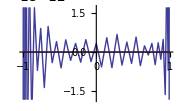

```mathematica
u''+SetLength[a,n] u'+SetLength[b,n] u-SetLength[f,n]
```

```mathematica
ConversionMatrix[1->2,n]//MatrixForm
```

(1 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | -1/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | -1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | 0 | -1/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/6 | 0 | -1/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/7 | 0 | -1/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/8 | 0 | -1/10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/9 | 0 | -1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/10 | 0 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | -1/13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/12 | 0 | -1/14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/13 | 0 | -1/15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/14 | 0 | -1/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/15 | 0 | -1/17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 | 0 | -1/18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/17 | 0 | -1/19 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | -1/20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/19 | 0 | -1/21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/20 | 0 | -1/22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/21 | 0 | -1/23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/22 | 0 | -1/24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/23 | 0 | -1/25 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/24 | 0 | -1/26 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/25 | 0 | -1/27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/26 | 0 | -1/28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/27 | 0 | -1/29 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/28 | 0 | -1/30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/29 | 0 | -1/31 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/30 | 0 | -1/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/31 | 0 | -1/33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/32 | 0 | -1/34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/33 | 0 | -1/35 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/34 | 0 | -1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/35 | 0 | -1/37 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | -1/38 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/37 | 0 | -1/39 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/38 | 0 | -1/40 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/39 | 0 | -1/41 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/40 | 0 | -1/42 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/41 | 0 | -1/43 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/42 | 0 | -1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/43 | 0 | -1/45
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/44 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/45)

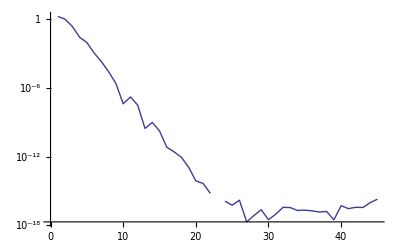

```mathematica
u//DCTPlot
```

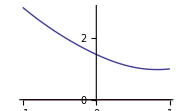

```mathematica
u=UltrasphericalSolve[a//DCT,b//DCT,{3,1},f//DCT]//InverseDCT//Fun
```

```mathematica
Timing[a=UltrasphericalSolve[al=Range[0,4]]]
```

{0.00018,{0.488604,-0.502508,-0.0194546,0.0167421,0.0405325,-0.0206584,-0.00982441,0.00685922,0.000293126,-0.000581009,-0.000166953,0.000169843,0.0000164067,-0.000025738,3.29936×10^-7,2.2736×10^-6,6.57296×10^-8,-3.98994×10^-7,1.00771×10^-8,4.19434×10^-8,-3.19253×10^-9,-3.41296×10^-9,3.22838×10^-10,4.41094×10^-10,-4.55209×10^-11,-3.66263×10^-11,5.19088×10^-12,2.66422×10^-12,-5.04701×10^-13,-2.78731×10^-13,4.81037×10^-14,1.93057×10^-14,-4.16034×10^-15,-1.24332×10^-15,3.59411×10^-16,1.11436×10^-16,-2.78233×10^-17,-6.57982×10^-18,2.04436×10^-18,3.71188×10^-19,-1.5747×10^-19,-2.97359×10^-20,1.05053×10^-20,1.49154×10^-21,-6.02003×10^-20,-6.4449×10^-21,4.37554×10^-21,5.22437×10^-22,-2.47318×10^-22,-3.10738×10^-23}}

We can compare the error with Mathematica:

```mathematica
<<Ultraspherical`
```

```mathematica
n=a//Length;Timing[amat=LinearSolve[Join[{DirichletOperator[-1]⟦1,;;n⟧,DirichletOperator[1]⟦1,;;n⟧},DerivativeMatrix[2,n]+ConversionMatrix[2,n].MultiplicationMatrix[al,n] //Most//Most],PadRight[{1,0},n]];]
```

{0.01878,Null}

```mathematica
amat-a//Norm
```

2.01477×10^-16